## Simple Particle Dynamics

### Initial Article

This source is taken from here (I have modified it for my understanding, but have not changed its function): https://mathematica.stackexchange.com/questions/161471/simulating-molecular-dynamics-efficiently

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
CCompilers[]
```

{{Name→Visual Studio,Compiler→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,CompilerInstallation→C:\Program Files\Microsoft Visual Studio\2022\Community,CompilerName→Automatic}}

```mathematica
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.(*diameter of one particle*);
Block[{r,x1,x2,y1,y2,xx,yy,force,potential},
(*xx & yy are each stand-ins for two dimensional vector.*)
xx={x1,x2};
yy={y1,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}];
With[
{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,  a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},(* All these N@s merely convert numbers to machine numbers. *)
(*This is the output: 
the symbol "getForces" becomes defined in the global environment. 
The Block and With protect symbols used to make the function.
Getforces will be passed a list of positions of particles nearest each particle.  Since it is listable, the function will iterate through the first level (i.e., particle by particle) and calculate the forces on each particle due to its nearest neighbors. *)
getForces=Compile[{{X,_Real,2}}, (* X is a list of particle positions. *)
Block[{x1,x2,y1,y2,f1,f2},x1=Compile`GetElement[X,1,1];
x2=Compile`GetElement[X,1,2];
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
f1+=f1code;
f2+=f2code;,{i,2,Length[X]}];
{f1,f2}],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]]]
```

CompiledFunction[…]

```mathematica
step=Function[x, (* Below, the symbols h & m are protected by Function *)
(* Nearest will return a list the length of x of all the particle locations (thus, a list of two elements) within epsilon of each member of x. *)
(* h^2/m could be precomputed.*)
(xnew=2. x-xold+h^2 (1./m) getForces[Nearest[x,x,{∞,epsilon}]];
xold=x;
xnew)];
```

```mathematica
SeedRandom[1234];
n=200;(*number of particules*)
h=0.01;(*time step*)
epsilon=10.;(* radius of influence*)
(*initial conditions*) 
(* With size=50, starts at {-48,-50} ... {48,-50}, {-50, -49} ... {-48, -49}, and so on, oddly ending with {-50,46}.*)
x0=N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;(*Initialize Verlet integration scheme*)
m(*particle masses*)=ConstantArray[1.,n ];
```

```mathematica
timesteps=10000;(* 10,000 in original.  Set to 1,000 to compare data to the speedup version,  would diverges starting around 400 steps.*)
xold=x0;
x=x1;
data=Join[{x0},NestList[step,x1,timesteps]];//AbsoluteTiming
```

{4.10837,Null}

```mathematica
frames=Map[X↦Graphics[{PointSize[1/size],Point[X]},PlotRange->box,PlotRangePadding->0.1 size],data];
Animate[frames⟦i⟧,{i,1,Length[frames],20}]
```

```mathematica
Export["a.gif",frames[[1;;-1;;20]]]
```

a.gif

```mathematica
SystemOpen["a.gif"]
```

```mathematica
xlo=Last[data];(*The last positions array.*)
```

Saving ‘data’ as we will use it as a reference.

```mathematica
Names["Global`*"]
```

```mathematica
ClearAll[x,x1,v0,x0,xold]
```

### Further Improvements

The same article had an improved version:

```mathematica
(* size=50.;(*size of the box*)box={{-size,size},{-size,size}};
r0=1.;*)(*diameter of one particle*)
Quiet[Block[{x1,x2,y1,y2,xx,yy,force,potential,r,r2},xx={x1,x2};
yy={y1,y2};
potential=r↦4 ((r0/r)^12-(r0/r)^6);
force=Simplify[-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}]/.(x1-y1)^2+(x2-y2)^2->r2]/.Sqrt[r2]->r;
With[{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},getStep=Compile[{{X,_Real,2},{Xold,_Real,1},{ilist,_Integer,1},{factor,_Real}},Block[{x1,x2,y1,y2,f1,f2,r,r2,j,i},j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
x2=Compile`GetElement[X,j,2];
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[i=Compile`GetElement[ilist,k];
y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
r2=(x1-y1)^2+(x2-y2)^2;
r=Sqrt[r2];
f1+=f1code;
f2+=f2code;,{k,2,Length[ilist]}];
{2. x1-Compile`GetElement[Xold,1]+factor f1,2. x2-Compile`GetElement[Xold,2]+factor f2}],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"]]]];
```

```mathematica
SeedRandom[1234];
n=1000; (* much larger *)(*number of particles*)
h=0.005;(*time step*)
epsilon=3.;(*radius of influence*)
(*initial conditions*)x0=Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}]];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;

m=ConstantArray[1.,n];(*particle masses*)factors=(h^2./m);
timesteps=10000;
skip=10;(*Nearest gets called only every 10th time iteration*)
```

Main loop:

```mathematica
datai=ConstantArray[0.,{timesteps+1,n,2}];(* changed name to datai to retain original data *)
datai[[1]]=x0;
datai[[2]]=x1;
xold=x0;
x=x1;
ilists=Nearest[x->Automatic,x,{∞,epsilon}];
Do[If[Mod[iter,skip]==0,ilists=Nearest[x->Automatic,x,{∞,epsilon}];];
datai[[iter]]=xnew=Developer`ToPackedArray[getStep[x,xold,ilists,factors]];
xold=x;
x=xnew;,{iter,3,timesteps+1}];//AbsoluteTiming
```

{4.21023,Null}

We’ll make a plot function instead of the script in the post:

```mathematica
plotData[v0_,data_,h_,r0_:1,size_,skip_:1]:=(* Fixed missing square on v0 *)
Module[{velocities=Sqrt[(Join[{v0},Differences[data]/h]^2).ConstantArray[1.,{2}]],colorcoords},
colorcoords=Rescale[Clip[velocities,{-100,100}]];
Table[Graphics[{PointSize[0.5 r0/size],Transpose[{ColorData["TemperatureMap"]/@colorcoords[[i]],Point/@data[[i]]}]
},PlotRange->box,PlotRangePadding->0.1 size,Background->Black],
{i,1,Length[data],skip}]];
```

```mathematica
framesi=plotData[v0,datai,h,r0,size,20];
```

```mathematica
Share[]
```

49338616

```mathematica
Animate[framesi[[i]],{i,1,Length[framesi],1}]
```

That wasn’t really a fair test, as it was 1,000 particles, not 200, a different potential, and with a different epsilon.  While it would not affect computation time, the timestep was different too.

```mathematica
ClearAll[datai,x,x0,x1,xold,v0,ilists,framesi]
```

#### Comparison to original

To compare to the original, we need to recast the entire function (to use the same potential).  We also had to remove the RunTimeOption “Speed”.

```mathematica
(* size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.;*)(*diameter of one particle*)
Block[{x1,x2,y1,y2,xx,yy,force,potential,r,r2},xx={x1,x2};
yy={y1,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=Simplify[-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}]/.(x1-y1)^2+(x2-y2)^2->r2]/.Sqrt[r2]->r;
With[{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},getStep1=Compile[{{X,_Real,2},{Xold,_Real,1},{ilist,_Integer,1},{factor,_Real}},Block[{x1,x2,y1,y2,f1,f2,r,r2,j,i},j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
x2=Compile`GetElement[X,j,2];
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[i=Compile`GetElement[ilist,k];
y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
r2=(x1-y1)^2+(x2-y2)^2;
r=Sqrt[r2];
f1+=f1code;
f2+=f2code;,{k,2,Length[ilist]}];
{2. x1-Compile`GetElement[Xold,1]+factor f1,
2. x2-Compile`GetElement[Xold,2]+factor f2}],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True(*,RuntimeOptions->"Speed"*)]]];
```

```mathematica
SeedRandom[1234];
n=200; (* number of particles*)
h=0.01;(* time step *)
epsilon=10.;(* radius of influence *)
(*initial conditions*)x0=Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}]];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;

m=ConstantArray[1.,n];(*particle masses*)
factors=(h^2./m);
timesteps=10000; (* Limit the number of steps *)
skip=1;(*Nearest gets called  every time iteration*)
```

```mathematica
?getStep1
```

Global`getStep1

getStep1=CompiledFunction[…]

Main loop:

```mathematica
datai2=ConstantArray[0.,{timesteps+2,n,2}];
datai2[[1]]=x0;
datai2[[2]]=x1;
xold=x0;
x=x1;
ilists=Nearest[x->Automatic,x,{∞,epsilon}];
Do[If[Mod[iter,skip]==0,ilists=Nearest[x->Automatic,x,{∞,epsilon}];];
datai2[[iter]]=xnew=Developer`ToPackedArray[getStep1[x,xold,ilists,factors]];
xold=x;
x=xnew;,{iter,3,timesteps+2}];//AbsoluteTiming
```

{2.43012,Null}

```mathematica
Length[frames]
```

10002

```mathematica
framesi2=plotData[v0,datai2,h,r0,size,1];
```

The two simulations look very close.

```mathematica
Animate[{i,frames⟦i⟧,framesi2[[i]]},{i,1,Length[frames],20}]
```

We can compare them element-by-element,

```mathematica
ddata=Norm/@(datai2-data);
```

The numerical errors start to accumulate as different particles make it inside epsilon..

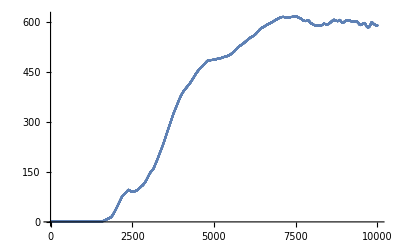

```mathematica
ListPlot[ddata]
```

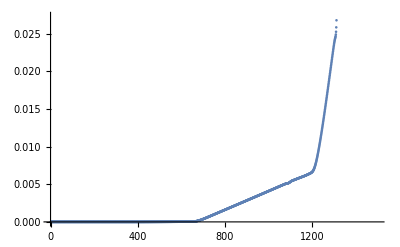

```mathematica
ListPlot[ddata⟦1;;1500⟧]
```

```mathematica
ClearAll[datai2,x0,x1,xold, framesi2]
```

```mathematica
Names["Global`*"]
```

{a1,a1$,a2,a2$,args,b1,b1$,b2,b2$,BitDepth,box,colorcoords,colorcoords$,colorcoords$20623,colorcoords$23700,colorcoords$9248,data,datai,datai2,data$,ddata,dims,epsilon,f1,f1code,f1code$,f2,f2code,f2code$,factor,factors,factor$,force,frames,framesc,framesi,framesi2,FullScreenArea,getForces,getStep,getStep1,h,h$,i,ilist,ilists,ilist$,iter,i$12618,i$12618$$,i$13453$$,i$16707$$,i$17060$$,i$22905,i$22905$$,i$23817,i$23817$$,i$40126$$,i$42996$$,i$4719$$,i$5373,i$5373$$,i$$,j,k,m,n,plotData,potential,r,r0,r0$,r2,Raster3DBoxOptionsImageEditMode,RasterBoxOptionsImageEditMode,Resolution,r$,ScreenArea,size,size$,skip,skip$,slope,slope$,step,timesteps,v0,v0$,velocities,velocities$,velocities$20620,velocities$9236,x,X,x0,x1,x2,xlo,xnew,xold,Xold,Xold$,xx,X$,y1,y2,yy}

## Renamed Variables

The variables had odd names, so I copied the above and started renaming variables.
xx, yy -> p1, p2 (we are calculating the force on point 1 by point 2)
x1, x2, y1, y2 -> x1, y1, x2, y2 for principle and i’th particle; x & y now refer to directions.  These symbols are reused.
f1code, f2code -> fxcode, fycode (directions)
a1, b1, a2, b2 -> bl, br, bb, bt (box left, right, bottom, top)
f1, f2 -> fx, fy

Within getForces,
x1, x2 -> xp, yp  (the principle point for which forces are being calculated)
y1, y2 -> xi, yi (the i’th point near principle point)

```mathematica
ClearAll[size,box,r0,getforces,step,n,h,epsilon,x0,v0,x1,m,data];
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.(*diameter of one particle*);
Block[{r,x1,x2,y1,y2,p1,p2,force,potential},
(*current & last are each stand-ins for two dimensional vector.*)
p1={x1,y1};
p2={x2,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
(* The subtraction need not be repeated. *)
(* 'force' will be a list of two elements, each the partial wrt the constituents of p1; {x1, y1}. *)
force=-D[potential[Sqrt[Dot[p1-p2,p1-p2]]],{p1,1}];
With[
{fxcode=N@force[[1]],fycode=N@force[[2]],slope=100.,  bl=N@box[[1,1]],br=N@box[[1,2]],bb=N@box[[2,1]],bt=N@box[[2,2]]},(* All these Ns merely convert numbers to machine numbers. *)
(*This is the output: 
the symbol "getForces" becomes defined in the global environment. 
The Block and With protect symbols used to make the function.
getForces will be passed the output of Nearest (see below), and since it is Listable, will be threadded over that list.  Thus, the input to getForces is a single list of the particles near particle i, whose location is first in the list (since its distance from itself is zero). *)
getForces=Compile[{{X,_Real,2}},Block[{x1,y1,x2,y2,fx,fy},
(* x1 & x2 have the x & y coordinate of particle i*)
x1=Compile`GetElement[X,1,1];
y1=Compile`GetElement[X,1,2];
(* f1 & f2 wil be the x & y forces on particle i.  This first claculation applies force from the walls, whichi are 'slope' times the distance past the edge of the walls. *)
fx=slope (Ramp[bl-x1]-Ramp[x1-br]);
fy=slope (Ramp[bb-y1]-Ramp[y1-bt]);
Do[x2=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
fx+=fxcode; (* 'fxcode' is an expression in terms of the symbols x1, y1, x2, & y2.*)
fy+=fycode;,{i,2,Length[X]}];
{fx,fy}],
CompilationTarget->"C",RuntimeAttributes->{Listable},
Parallelization->True,RuntimeOptions->"Speed"]]]
```

CompiledFunction[…]

```mathematica
step=Function[x,(* The Nearest call will return a list of n lists, list i containing a list of all the particle locations sorted by distance, starting with particle i itself (which has distance zero from itself).*)
(xnew=2. x-xold+h^2 (1./m) getForces[Nearest[x,x,{∞,epsilon}]];
xold=x;
xnew)];
```

```mathematica
SeedRandom[1234];
n=200;(*number of particles*)
h=0.01;(*time step*)
epsilon=10.;(*radius of influence*)
(*initial conditions*) 
(* With size=50, starts at {-48,-50} ... {48,-50}, {-50, -49} ... {-48, -49}, and so on, oddly ending with {-50,46}.*)
x0=N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;(*Initialize Verlet integration scheme*)
m(*particle masses*)=ConstantArray[1.,n ];
```

```mathematica
timesteps=10000;
xold=x0;
x=x1;
data=Join[{x0},NestList[step,x1,timesteps]];//AbsoluteTiming
```

{3.54623,Null}

```mathematica
framer=Table[Graphics[{PointSize[1/size],Point[data⟦i⟧]},PlotRange->box,PlotRangePadding->0.1 size],{i,1,Length[data]}];
```

```mathematica
Animate[framer⟦i⟧,{i,1,Length[framer],1}]
```

### Further Improvements

We’ll do the same renaming to the improved version.

```mathematica
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.;(*diameter of one particle*)
Block[{x1,x2,y1,y2,p1,p2,force,potential,r,r2},p1={x1,y1};
p2={x2,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=Simplify[-D[potential[Sqrt[Dot[p1-p2,p1-p2]]],{p1,1}]/.(x1-x2)^2+(y1-y2)^2->r2]/.Sqrt[r2]->r;
With[{fxcode=N@force[[1]],fycode=N@force[[2]],slope=100.,bl=N@box[[1,1]],br=N@box[[1,2]],bb=N@box[[2,1]],bt=N@box[[2,2]]},getStep1=Compile[{{X,_Real,2},{Xold,_Real,1},{ilist,_Integer,1},{factor,_Real}},Block[{x1,x2,y1,y2,fx,fy,r,r2,j,i},j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
y1=Compile`GetElement[X,j,2];
fx=slope (Ramp[bl-x1]-Ramp[x1-br]);
fy=slope (Ramp[bb-y1]-Ramp[y1-bt]);
Do[i=Compile`GetElement[ilist,k];
x2=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
r2=(x1-x2)^2+(y1-y2)^2;
r=Sqrt[r2];
fx+=fxcode;
fy+=fycode;,{k,2,Length[ilist]}];
{2. x1-Compile`GetElement[Xold,1]+factor fx,
2. y1-Compile`GetElement[Xold,2]+factor fy}],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True(*,RuntimeOptions->"Speed"*)]]];
```

```mathematica
SeedRandom[1234];
n=200; (* much larger *)(*number of particules*)
h=0.01;(*time step*)
epsilon=10.;(*radius of influence*)
(*initial conditions*)x0=Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}]];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;

m=ConstantArray[1.,n];(*particle masses*)
factors=(h^2./m);
timesteps=1000; (* Limit the number of steps *)
skip=1;(*Nearest gets called  every time iteration*)
```

```mathematica
?getStep1
```

Global`getStep1

getStep1=CompiledFunction[…]

Main loop:

```mathematica
datai=ConstantArray[0.,{timesteps+2,n,2}];
datai[[1]]=x0;
datai[[2]]=x1;
xold=x0;
x=x1;
ilists=Nearest[x->Automatic,x,{∞,epsilon}];
Do[If[Mod[iter,skip]==0,ilists=Nearest[x->Automatic,x,{∞,epsilon}];];
datai[[iter]]=xnew=Developer`ToPackedArray[getStep1[x,xold,ilists,factors]];
xold=x;
x=xnew;,{iter,3,timesteps+2}];//AbsoluteTiming
```

{0.289231,Null}

```mathematica
velocities=Sqrt[(Join[{v0},Differences[datai]/h]^2).ConstantArray[1.,{2}]];
colorcoords=Rescale[Clip[velocities,{-100,100}]];
framesi=Table[Graphics[{PointSize[0.5 r0/size],Transpose[{ColorData["TemperatureMap"]/@colorcoords[[i]],Point/@datai[[i]]}],},PlotRange->box,PlotRangePadding->0.1 size,Background->Black],{i,1,Length[datai]}];
```

The two simulations look very close.

```mathematica
Animate[{i,frames⟦i⟧,framesi[[i]]},{i,1,Length[framesi],1}]
```

We can compare them element-by-element.

```mathematica
ddata=datai-data;
```

The numerical errors start to accumulate.

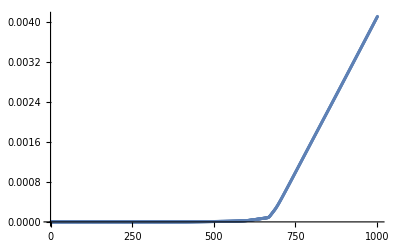

```mathematica
ListPlot[Norm/@ddata]
```

## Getting Production Code

The code above uses parameters from the environment in several different ways, and these all need to be regularized.  The target is to be able to save a configuration to a file, and continue the simulation by reading the data from a file and adding more steps, possibly with some changes.

The parameters come in a few flavors.  Some are essentially hardwired into the compiled code, specifically the box size and shape,  and the potential function is also hardwired.  Also, the symbol in which the compiled function is contained is in the OwnValues of a symbol declared in the code. 

Below we make the compiled function creation a function of those  parameters, and also of the potential function.

```mathematica
createStepFn[potential_,size_Real:50.0, boxRatio_Real:1.0]:=(*size is the size of the x side of the box, boxRatio is the multiplier of the y side. *)
Module[ {box={{-size,size},boxRatio{-size,size}}},
(* r0=1.; diameter of one particle*)
Block[{x1,x2,y1,y2,p1,p2,force,r,r2},p1={x1,y1};
p2={x2,y2};
force=Simplify[-D[potential[Sqrt[Dot[p1-p2,p1-p2]]],{p1,1}]/.(x1-x2)^2+(y1-y2)^2->r2]/.Sqrt[r2]->r;
With[{fxcode=N@force[[1]],fycode=N@force[[2]],slope=100.,bl=N@box[[1,1]],br=N@box[[1,2]],bb=N@box[[2,1]],bt=N@box[[2,2]]},getStep1=Compile[{{X,_Real,2},{Xold,_Real,1},{ilist,_Integer,1},{factor,_Real}},Block[{x1,x2,y1,y2,fx,fy,r,r2,j,i},
j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
y1=Compile`GetElement[X,j,2];
fx=slope (Ramp[bl-x1]-Ramp[x1-br]);
fy=slope (Ramp[bb-y1]-Ramp[y1-bt]);
Do[i=Compile`GetElement[ilist,k];
x2=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
r2=(x1-x2)^2+(y1-y2)^2;
r=Sqrt[r2];
fx+=fxcode;
fy+=fycode;,
{k,2,Length[ilist]}];
{2. x1-Compile`GetElement[Xold,1]+factor fx,
2. y1-Compile`GetElement[Xold,2]+factor fy}],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"]]]]
```

```mathematica
potential=1/4 ((1/#)^2-(1/#))&
```

1/4 ((1/#1)^2-1/#1)&

```mathematica
getStep2=createStepFn[potential,50.0]
```

CompiledFunction[…]

We need to create the initial system state:

```mathematica
SeedRandom[1234];
systemState=<|"n"->200,(*number of particules*)
"h"->0.01,(*time step*)
"epsilon"->10.,(*radius of influence*)
"m"->1.0,(* Particle mass *)
"stepFun"->getStep2,(* Try to store in data. *)
"skip"->1,(* The number of steps between Nearest calls *)
"x0"->Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}]],"v0"->0.1 size RandomReal[{-1,1},{n,2}]|>;
```

A function to run the code will be convenient too.

```mathematica
execSteps[ timesteps_Integer,ss_Association]:=Module[
{n=ss["n"],h=ss["h"],epsilon=ss["epsilon"],m=ss["m"],factors=ss["h"]^2/ss["m"],x0=ss["x0"],x1=ss["x0"]+ss["h"] ss["v0"], xold=ss["x0"],x,xnew,v0=ss["v0"],skip=ss["skip"],data=ConstantArray[0.,{timesteps+2,n,2}],ilists,ssr=ss},
(*ilists=Nearest[x->"Index",x,{∞,epsilon}];*)
data⟦1⟧=x0;
data⟦2⟧=x1;
x=x1;
Do[If[Mod[iter,skip]==0,ilists=Nearest[x->"Index",x,{∞,epsilon}];];
data[[iter+3]]=xnew=Developer`ToPackedArray[ss["stepFun"][x,xold,ilists,factors]];
xold=x;
x=xnew;,
{iter,0,timesteps-1}];
ssr["x0"]=Last[data];
ssr["v0"]=(data⟦timesteps+2⟧-data⟦timesteps+1⟧);
{ssr,data}]
```

```mathematica
?execSteps
```

Global`execSteps

execSteps[timesteps_Integer,ss_Association]:=Module[{n=ss[n],h=ss[h],epsilon=ss[epsilon],m=ss[m],factors=ss[h]^2/ss[m],x0=ss[x0],x1=ss[x0]+ss[h] ss[v0],xold=ss[x0],x,xnew,v0=ss[v0],skip=ss[skip],data=ConstantArray[0.,{timesteps+2,n,2}],ilists,ssr=ss},data⟦1⟧=x0;data⟦2⟧=x1;x=x1;Echo[x⟦1⟧];Do[If[Mod[iter,skip]==0,ilists=Nearest[x→Index,x,{∞,epsilon}];];data⟦iter+3⟧=xnew=Developer`ToPackedArray[ss[stepFun][x,xold,ilists,factors]];xold=x;x=xnew;,{iter,0,timesteps-1}];ssr[x0]=Last[data];ssr[v0]=data⟦timesteps+2⟧-data⟦timesteps+1⟧;{ssr,data}]

Execute the code:

```mathematica
t=execSteps[1000,systemState]//AbsoluteTiming;
```

{-47.9623,-49.9978}

```mathematica
t⟦1⟧
```

0.514474

```mathematica
Length[t⟦2,2,1⟧]
```

200

```mathematica
t⟦2,2,3⟧;
```

```mathematica
ddata=t⟦2,2⟧-data;
```

The numerical errors still accumulate.

```mathematica
(* ddata=datan-data;*)
```

```mathematica
ListPlot[Norm/@ddata]
```

-Graphics-

If we increase the step size it will increase the error

```mathematica
systemState["skip"]=2;
t=execSteps[1000,systemState]//AbsoluteTiming;
```

{-47.9623,-49.9978}

```mathematica
ddata=t⟦2,2⟧-data;
```

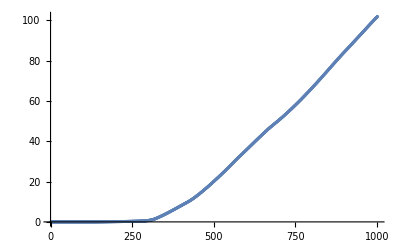

```mathematica
ListPlot[Norm/@ddata]
```

```mathematica
t=execSteps[10000,systemState]//AbsoluteTiming;
```

```mathematica
t
```

## Playground

```mathematica
OwnValues[getStep1]
```

{HoldPattern[getStep1]:>CompiledFunction[…]}

```mathematica
Sin@Pi
```

```mathematica
ClearAll[r,x1,x2,y1,y2,xx,yy,force,potential]
```

```mathematica
xx={x1,x2};
yy={y1,y2};potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}];
```

```mathematica
N@force⟦1⟧
```

0.25 ((2. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^2)-(1. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^(3/2)))

```mathematica
force[[2]]
```

1/4 ((2. (x2-y2))/(((x1-y1)^2+(x2-y2)^2)^2)-(1. (x2-y2))/(((x1-y1)^2+(x2-y2)^2)^(3/2)))

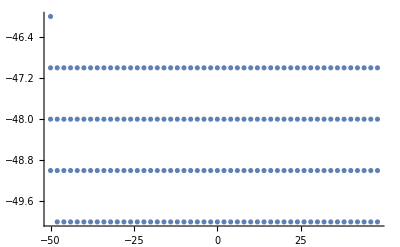

```mathematica
ListPlot[x0]
```

```mathematica
x0
```

{{-48.,-50.},{-46.,-50.},{-44.,-50.},{-42.,-50.},{-40.,-50.},{-38.,-50.},{-36.,-50.},{-34.,-50.},{-32.,-50.},{-30.,-50.},{-28.,-50.},{-26.,-50.},{-24.,-50.},{-22.,-50.},{-20.,-50.},{-18.,-50.},{-16.,-50.},{-14.,-50.},{-12.,-50.},{-10.,-50.},{-8.,-50.},{-6.,-50.},{-4.,-50.},{-2.,-50.},{0.,-50.},{2.,-50.},{4.,-50.},{6.,-50.},{8.,-50.},{10.,-50.},{12.,-50.},{14.,-50.},{16.,-50.},{18.,-50.},{20.,-50.},{22.,-50.},{24.,-50.},{26.,-50.},{28.,-50.},{30.,-50.},{32.,-50.},{34.,-50.},{36.,-50.},{38.,-50.},{40.,-50.},{42.,-50.},{44.,-50.},{46.,-50.},{48.,-50.},{-50.,-49.},{-48.,-49.},{-46.,-49.},{-44.,-49.},{-42.,-49.},{-40.,-49.},{-38.,-49.},{-36.,-49.},{-34.,-49.},{-32.,-49.},{-30.,-49.},{-28.,-49.},{-26.,-49.},{-24.,-49.},{-22.,-49.},{-20.,-49.},{-18.,-49.},{-16.,-49.},{-14.,-49.},{-12.,-49.},{-10.,-49.},{-8.,-49.},{-6.,-49.},{-4.,-49.},{-2.,-49.},{0.,-49.},{2.,-49.},{4.,-49.},{6.,-49.},{8.,-49.},{10.,-49.},{12.,-49.},{14.,-49.},{16.,-49.},{18.,-49.},{20.,-49.},{22.,-49.},{24.,-49.},{26.,-49.},{28.,-49.},{30.,-49.},{32.,-49.},{34.,-49.},{36.,-49.},{38.,-49.},{40.,-49.},{42.,-49.},{44.,-49.},{46.,-49.},{48.,-49.},{-50.,-48.},{-48.,-48.},{-46.,-48.},{-44.,-48.},{-42.,-48.},{-40.,-48.},{-38.,-48.},{-36.,-48.},{-34.,-48.},{-32.,-48.},{-30.,-48.},{-28.,-48.},{-26.,-48.},{-24.,-48.},{-22.,-48.},{-20.,-48.},{-18.,-48.},{-16.,-48.},{-14.,-48.},{-12.,-48.},{-10.,-48.},{-8.,-48.},{-6.,-48.},{-4.,-48.},{-2.,-48.},{0.,-48.},{2.,-48.},{4.,-48.},{6.,-48.},{8.,-48.},{10.,-48.},{12.,-48.},{14.,-48.},{16.,-48.},{18.,-48.},{20.,-48.},{22.,-48.},{24.,-48.},{26.,-48.},{28.,-48.},{30.,-48.},{32.,-48.},{34.,-48.},{36.,-48.},{38.,-48.},{40.,-48.},{42.,-48.},{44.,-48.},{46.,-48.},{48.,-48.},{-50.,-47.},{-48.,-47.},{-46.,-47.},{-44.,-47.},{-42.,-47.},{-40.,-47.},{-38.,-47.},{-36.,-47.},{-34.,-47.},{-32.,-47.},{-30.,-47.},{-28.,-47.},{-26.,-47.},{-24.,-47.},{-22.,-47.},{-20.,-47.},{-18.,-47.},{-16.,-47.},{-14.,-47.},{-12.,-47.},{-10.,-47.},{-8.,-47.},{-6.,-47.},{-4.,-47.},{-2.,-47.},{0.,-47.},{2.,-47.},{4.,-47.},{6.,-47.},{8.,-47.},{10.,-47.},{12.,-47.},{14.,-47.},{16.,-47.},{18.,-47.},{20.,-47.},{22.,-47.},{24.,-47.},{26.,-47.},{28.,-47.},{30.,-47.},{32.,-47.},{34.,-47.},{36.,-47.},{38.,-47.},{40.,-47.},{42.,-47.},{44.,-47.},{46.,-47.},{48.,-47.},{-50.,-46.}}

```mathematica
box
```

{{-50.,50.},{-50.,50.}}

```mathematica
t=Nearest[x0,x0,{∞,epsilon}];
```

```mathematica
Length[t]
```

200

```mathematica
Dimensions[t]
```

{200}

```mathematica
t⟦1⟧
```

{{-48.,-50.},{-48.,-49.},{-46.,-50.},{-48.,-48.},{-50.,-49.},{-46.,-49.},{-50.,-48.},{-46.,-48.},{-48.,-47.},{-50.,-47.},{-46.,-47.},{-44.,-50.},{-44.,-49.},{-44.,-48.},{-50.,-46.},{-44.,-47.},{-42.,-50.},{-42.,-49.},{-42.,-48.},{-42.,-47.},{-40.,-50.},{-40.,-49.},{-40.,-48.},{-40.,-47.},{-38.,-50.}}

```mathematica
t⟦2⟧
```

{{-46.,-50.},{-46.,-49.},{-48.,-50.},{-44.,-50.},{-46.,-48.},{-48.,-49.},{-44.,-49.},{-48.,-48.},{-44.,-48.},{-46.,-47.},{-48.,-47.},{-44.,-47.},{-42.,-50.},{-50.,-49.},{-42.,-49.},{-50.,-48.},{-42.,-48.},{-50.,-47.},{-42.,-47.},{-50.,-46.},{-40.,-50.},{-40.,-49.},{-40.,-48.},{-40.,-47.},{-38.,-50.},{-38.,-49.},{-38.,-48.},{-38.,-47.},{-36.,-50.}}

```mathematica
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.(*diameter of one particle*);
Block[{r,x1,x2,y1,y2,xx,yy,force,potential},
(*xx & yy are each stand-ins for two dimensional vector.*)
xx={x1,x2};
yy={y1,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}];
With[
{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,  a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},(* All these Ns merely convert numbers to machine numbers. *)

(*This is the output: 
the symbol "getForces" becomes defined in the global environment. 
The Block and With protect symbols used to make the function.
Getforces will be passed a list of positions of particles nearest each particle.  Since it is listable, the function will iterate through the first level (i.e., particle by particle) and calculate the forces on each particle due to its nearest neighbors. *)
getForcesnc=Function[X, (* X is a list of particle positions. *)
Block[{x1,x2,y1,y2,f1,f2},x1=X⟦1,1⟧;
x2=X⟦1,2⟧;
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
f1+=f1code;
f2+=f2code;,{i,2,Length[X]}];
{f1,f2}]]]]
```

Function[X$,Block[{x1,x2,y1,y2,f1,f2},x1=X$⟦1,1⟧;x2=X$⟦1,2⟧;f1=100. (Ramp[-50.-x1]-Ramp[x1-50.]);f2=100. (Ramp[-50.-x2]-Ramp[x2-50.]);Do[y1=Compile`GetElement[X$,i,1];y2=Compile`GetElement[X$,i,2];f1+=0.25 ((2. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^2)-(1. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^(3/2)));f2+=0.25 ((2. (x2-1. y2))/(((x1-1. y1)^2+(x2-1. y2)^2)^2)-(1. (x2-1. y2))/(((x1-1. y1)^2+(x2-1. y2)^2)^(3/2)));,{i,2,Length[X$]}];{f1,f2}]]

```mathematica
getForcesnc[Nearest[x0,x0⟦1⟧,{∞,epsilon}]]
```

{0.052651,-0.188322}

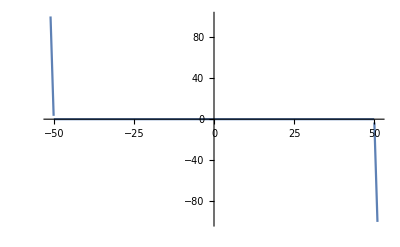

```mathematica
With[{slope=100, bl=-50,br=50},Plot[slope (Ramp[bl-x1]-Ramp[x1-br]),{x1,-51,51}]]
```

```mathematica
cP=Compile[{{x}},
Module[{sum=1.0,inc=1.0},Do[inc=inc*x/i;sum=sum+inc,{i,100000}];sum*x],
RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];
arg=Range[ -50.,50, 0.01];
cP[arg];//AbsoluteTiming

cP2=Compile[{{x}},
Module[{sum=1.0,inc=1.0},Do[inc=inc*x/i;sum=sum+inc,{i,100000}];sum*x],
RuntimeAttributes->{Listable},Parallelization->False,CompilationTarget->"C"];
cP2[arg];//AbsoluteTiming
```

{0.397341,Null}

{1.14253,Null}

```mathematica
Length[arg]
```

5001

```mathematica
ClearAll[cP,cP2,arg]
```

{1.33936,Null}